# Quantum Teleportation

Referencespaclet:Q3/tutorial/QuantumTeleportation#1175517547 | Quantum Circuit Modelpaclet:Q3/tutorial/QuantumTeleportation#1178477808

Quantum teleportation is a quantum communication protocol to transmit quantum states between remotely separated parties using pre-shared entangled pairs and classical channels. Unlike teleportation which is commonly depicted in science fiction, quantum teleportation does not transfer the object (matter) itself but only information.

Quantum teleportation was first investigated by C. H. Bennet and his collaborators in 1993 [1].

Here we demonstrate the quantum teleportation using the Q3 Application.

QuantumCircuit | Circuit representation of elementary gates
CNOT | Two-qubit controlled-NOT gate
Matrix | Converts QuantumCircuit and operator (or Ket) expressions to the matrix representation in the standard basis.
ExpressionFor | Converts the matrix representation to the corresponding operator or state-vector expression.

Functions used in the demonstration of the quantum teleportation protocol.

## References

[1] C. H. Bennet, G. Brassard, C. Crepeau, R. Jozsa, A. Peres, and W. K. Wootters, "Teleporting an Unknown Quantum State via Dual Classical and Einstein-Podolsky-Rosen Channels," Physical Review Letters 70 (13), 1895 (1993).

## Quantum Circuit Model

Start with loading the package

```mathematica
<<Q3`
```

Choose the symbol to denote the Qubitspaclet:Q3/ref/Qubits.

```mathematica
Let[Qubit,S]
```

Bob chooses an arbitrary state to teleport to Alice, and prepare the third Qubitpaclet:Q3/ref/Qubit S[3,None] in it.

```mathematica
Let[Complex,c]
in=ProductState[S[3]->c@{0,1},"Label"->Ket[ψ]]
```

(c_0 0+c_1 1)_S_3

Here is a quantum circuit model of quantum teleportation. The first, S[1,None], qubit belongs to Alice whereas Bob holds the two qubits S[2,None] and S[3,Non]. There is no notion of spatial distance in quantum circuit model. In the model below, extra space is inserted between the first qubit and the rest just to simulate the spatial distance.

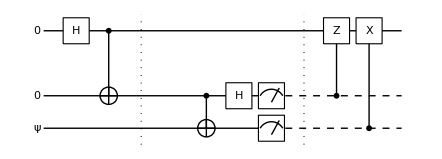

```mathematica
qc=QuantumCircuit[
in,LogicalForm[Ket[],S@{1,2}],
S[1,6],CNOT[S[1],S[2]],"Separator","Spacer",
CNOT[S[2],S[3]],
S[2,6],{Measurement[S[2]],Measurement[S[3]]},"Separator",
ControlledU[S[2],S[1,3]],ControlledU[S[3],S[1,1]],
"Invisible"->S[1.5]
]
```

Convert the quantum circuit model (represented by QuantumCircuitpaclet:Q3/ref/QuantumCircuit) to an operator expression by means of either ExpresssionForpaclet:Q3/ref/ExpressionFor or Matrixpaclet:Q3/ref/Matrix (usually faster).

```mathematica
outAll=ExpressionFor[qc]/.{c[0]*Conjugate[c[0]]+c[1]*Conjugate[c[1]]->1}//Simplify
```

c_1 1_S_11_S_3+c_0 1_S_3

Let us examine the state in Alice’s qubit (S[1,None]).

```mathematica
out=Last@QuissoFactor[outAll,S[{2,3}]]//Simplify;
out//LogicalForm
```

c_0 0_S_1+c_1 1_S_1

As quantum teleportation is deterministic, the result of the Bell measurement by Bob does not matter.

```mathematica
out=Table[ExpressionFor[qc],{10}]/.c[0]*Conjugate[c[0]]+c[1]*Conjugate[c[1]]->1;
QuissoFactor[#,S@{2,3}]&/@out//LogicalForm//TableForm
```

0_S_20_S_3⊗(c_0 0_S_1+c_1 1_S_1)
1_S_21_S_3⊗(c_0 0_S_1+c_1 1_S_1)
1_S_21_S_3⊗(c_0 0_S_1+c_1 1_S_1)
0_S_21_S_3⊗(c_0 0_S_1+c_1 1_S_1)
1_S_21_S_3⊗(c_0 0_S_1+c_1 1_S_1)
0_S_21_S_3⊗(c_0 0_S_1+c_1 1_S_1)
1_S_21_S_3⊗(c_0 0_S_1+c_1 1_S_1)
1_S_21_S_3⊗(c_0 0_S_1+c_1 1_S_1)
0_S_21_S_3⊗(c_0 0_S_1+c_1 1_S_1)
1_S_21_S_3⊗(c_0 0_S_1+c_1 1_S_1)

For heuristic purposes, let us also take a look at Bob’s measurement statistics.

```mathematica
{c[0],c[1]}=Normalize@RandomVector[2]
```

{0.428839+0.416852 ⅈ,0.444534-0.666874 ⅈ}

```mathematica
val=Table[
out=ExpressionFor[qc]//Simplify;
Readout[out,S[{2,3}]],
{100}
];
Histogram3D[val]
```

-Graphics3D-

In the above example, the statistical distribution is not completely uniform. You can try with an increased number of repetitions. However, the point is that regardless of the statistical distribution of the measurement outcomes, the teleportation protocol is always successful.

Related Guides

Quisso Package Guide

Related Tutorials

QuantumCircuit Usage Examples

Quisso: Quick Start

Related Wolfram Education Group Courses

An Elementary Introduction to the Wolfram Languagehttps://www.wolfram.com/language/elementary-introduction/

The Wolfram Language: Fast Introduction for Programmershttps://www.wolfram.com/language/fast-introduction-for-programmers/